```mathematica
SetOptions[ListPlot,Joined->True,Frame->True,BaseStyle->{14,PrivateFontOptions->{"OperatorSubstitution"->False}},Axes->False,LabelStyle->Directive[FontFamily->"Helvetica"],FrameStyle->Thick,ImageSize->{450,Automatic},ImagePadding->{{60,20},{45,10}}];
SetOptions[MatrixPlot,Frame->True,BaseStyle->{14,PrivateFontOptions->{"OperatorSubstitution"->False}},Axes->False,LabelStyle->Directive[FontFamily->"Helvetica"],FrameStyle->Thick,ImageSize->{450,Automatic},ImagePadding->{{60,20},{45,10}}];
```

```mathematica
SetDirectory["/home/felix/Dropbox/vafmpro/pyvafm/examples"];
```

```mathematica
files={"rsaamp_0.out","rsaamp_0.1.out","rsaamp_1.1.out","rsaamp_5.1.out","rsaamp_10.1.out","rsaamp_20.1.out","rsaamp_50.1.out","rsaamp_100.1.out","rsaamp_200.1.out","rsaamp_500.1.out","rsaamp_1000.1.out"};
data=Import[#,"Table"]&/@files;
data[[All,All,{2,3,4}]]*=1000;
```

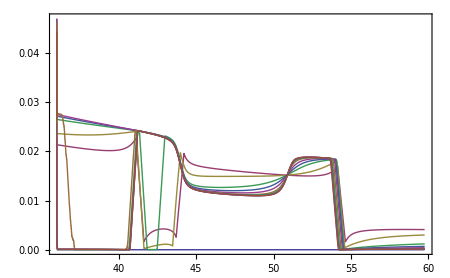

```mathematica
ListPlot[
Table[data[[i,All,{1,2}]],{i,Length[files]}]
,PlotRange->All,Joined->True,Frame->True,Axes->False]
ListPlot[Table[data[[i,All,{1,3}]],{i,Length[files]}],PlotRange->All,Joined->True,Frame->True,Axes->False]
ListPlot[Table[MovingAverage[data[[i,All,{1,4}]],100],{i,Length[files]}],PlotRange->All,Joined->True,Frame->True,Axes->False]
ListPlot[Table[MovingAverage[data[[i,All,{1,5}]],100],{i,Length[files]}],PlotRange->All,Joined->True,Frame->True,Axes->False]
```

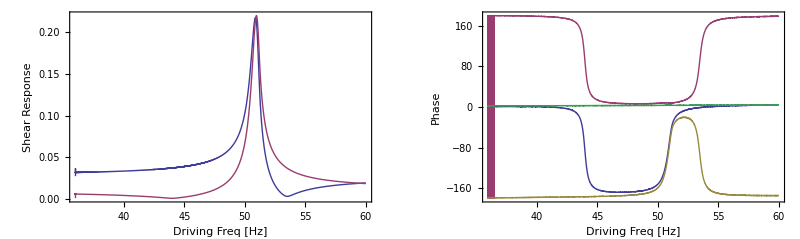

```mathematica
idx=8;
tmp=data[[idx,30;;,{1,5}]];
tmp[[All,2]]=Mod[(2Pi tmp[[All,1]])*tmp[[All,2]]180/Pi,360];
tmp[[All,2]]=If[#>180,#-360,#]&/@tmp[[All,2]];
tmp2=data[[idx,30;;,{1,6}]];
tmp2[[All,2]]=Mod[(2Pi tmp2[[All,1]])*tmp2[[All,2]]180/Pi,360];
tmp2[[All,2]]=If[#>180,#-360,#]&/@tmp2[[All,2]];
tmp3=data[[idx,30;;,{1,7}]];
tmp3[[All,2]]=Mod[(2Pi tmp3[[All,1]])*tmp3[[All,2]]180/Pi,360];
tmp3[[All,2]]=If[#>180,#-360,#]&/@tmp3[[All,2]];
tmp4=data[[idx,30;;,{1,8}]];
tmp4[[All,2]]=Mod[(2Pi tmp4[[All,1]])*tmp4[[All,2]]180/Pi,360];
tmp4[[All,2]]=If[#>180,#-360,#]&/@tmp4[[All,2]];
GraphicsRow[{
ListPlot[{data[[idx,1;;,{1,2}]],data[[idx,1;;,{1,3}]]},PlotRange->All,Joined->True,Frame->True,Axes->False,PlotStyle->Thick,FrameLabel->{"Driving Freq [Hz]","Shear Response"}],
ListPlot[{tmp,tmp2,tmp3,tmp4},PlotRange->All,Joined->True,Frame->True,Axes->False,PlotStyle->Thick,FrameLabel->{"Driving Freq [Hz]","Phase"}]
},ImageSize->800]
Export["run_"<>ToString[idx]<>"_resp.png",%,"PNG"];
```

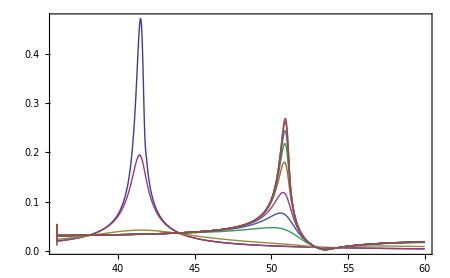

run2_topshear.png

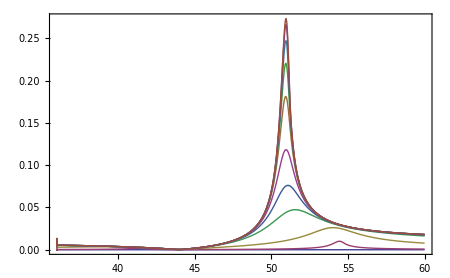

run2_lowshear.png

```mathematica
ListPlot[
Table[data[[i,All,{1,2}]],{i,Length[files]}]
,PlotRange->All,Joined->True,Frame->True,Axes->False]
Export["run2_topshear.png",%,"PNG"]
ListPlot[
Table[data[[i,All,{1,3}]],{i,Length[files]}]
,PlotRange->All,Joined->True,Frame->True,Axes->False]
Export["run2_lowshear.png",%,"PNG"]
```

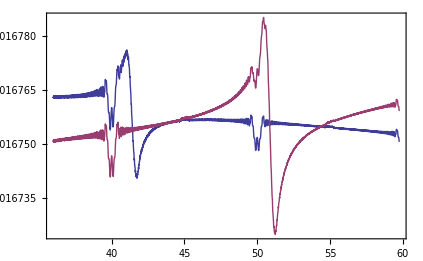

```mathematica
ListPlot[Table[MovingAverage[data[[i,All,{1,4}]],100],{i,{1,-1}}],PlotRange->All,Joined->True,Frame->True,Axes->False]
```

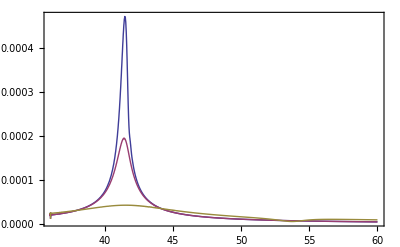

```mathematica
ListPlot[data[[1;;3,All,{1,2}]],PlotRange->All,Joined->True,Frame->True,Axes->False]
```